```mathematica
filesAR=FileNames["/home/carla//GDC/CONF/AUS/GDC_Conf_AR_AUS_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla//GDC/CONF/AUS/GDC_Conf_BR_AUS_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]];
confBR=dataBR[[All,1]];
```

```mathematica
dojAR=confAR[[All,1]][[All,1]];
zAR=confAR[[All,2]][[All,1]];
fAR=confAR[[All,3]][[All,1]];
```

```mathematica
dojBR=confBR[[All,1]][[All,1]]
zBR=confBR[[All,2]][[All,1]]
fBR=confBR[[All,3]][[All,1]]
```

{0.0162602,0.2}

{0.0144362,0.19851}

{0.798284,0.985212}

```mathematica
sList={6,7,8};
sList2={6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];


dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
zPAR= {#[[2]],#[[1]]}&/@Map[{zAR[[#]],sList[[#]]}&,ran];
fPAR= {#[[2]],#[[1]]}&/@Map[{fAR[[#]],sList[[#]]}&, ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&, ran2];
zPBR= {#[[2]],#[[1]]}&/@Map[{zBR[[#]],sList2[[#]]}&, ran2];
fPBR= {#[[2]],#[[1]]}&/@Map[{fBR[[#]],sList2[[#]]}&, ran2];
```

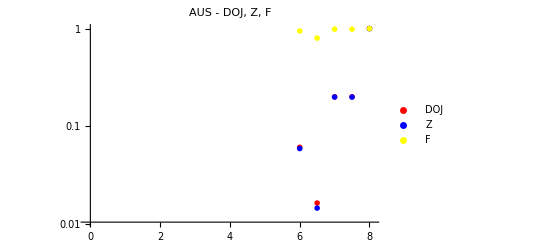

```mathematica
PlotAllParts=ListLogPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotRange->{{-0.1,8.1},All},PlotStyle-> {Red, Blue, Yellow}, PlotRange->All, PlotLabel->"AUS - DOJ, Z, F", PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

```mathematica
SetDirectory["/home/carla//GDC/CONF/AUS/"];
Put[Union[dojPAR,dojPBR],"AUS_DOJ.txt"]
Put[Union[zPAR,zPBR],"AUS_Z.txt"]
Put[Union[fPAR,fPBR],"AUS_F.txt"]
Export["AUS.jpeg",PlotAllParts,ImageSize->800, ImageResolution->300]
```

AUS.jpeg

```mathematica
(*PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{0, 0.2},  PlotLabel->"AUS - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
Export["AUS_Zoomed_In.jpeg",PlotParts,ImageSize->850]*)
```